```mathematica
h:=-f √(Ja Jb)Cos[ϕa-ϕb+2 δ/R]+δ/R(Ja-Jb)
```

```mathematica
FullSimplify[-D[h,ϕa]]
```

-f √(Ja Jb) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Ja]]
```

δ/R-(f Jb Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
FullSimplify[-D[h,ϕb]]
```

f √(Ja Jb) Sin[(2 δ)/R+ϕa-ϕb]

```mathematica
FullSimplify[D[h,Jb]]
```

-δ/R-(f Ja Cos[(2 δ)/R+ϕa-ϕb])/(2 √(Ja Jb))

```mathematica
hh=FullSimplify[h/.{Ja->(II+J)/2,Jb->(II-J)/2,ϕa->ϕb-(2 δ)/R+Φ}]
```

(J δ)/R-1/2 f √((II-J) (II+J)) Cos[Φ]

```mathematica
Simplify[PowerExpand[Simplify[Series[hh/.{J->J1,Φ->d ϕ},{d,0,2}]]]]
```

-(II √(f^2 R^2+4 δ^2))/(2 R)+((8 f^2 j^2 R^2 δ^2+16 j^2 δ^4+f^4 R^4 (j^2+II^2 ϕ^2)) d^2)/(4 f^2 II R^3 √(f^2 R^2+4 δ^2))+O[d]^3

```mathematica
сф=f^4 R^4 II^2 d^2/(4 f^2 II R^3 √(f^2 R^2+4 δ^2));
```

```mathematica
cj=d^2(8 f^2 R^2 δ^2+16 δ^4+f^4 R^4 )/(4 f^2 II R^3 √(f^2 R^2+4 δ^2));
```

```mathematica
PowerExpand[Simplify[PowerExpand[2 Sqrt[сф cj]]]]
```

(d^2 √(f^2 R^2+4 δ^2))/(2 R)

```mathematica
H=H0+P^2/(2m)+k x^2/2
```

H0+P^2/(2 m)+(k x^2)/2

```mathematica
JStr=FullSimplify[-D[hh,Φ]]
```

-1/2 f √((II-J) (II+J)) Sin[Φ]

```mathematica
1/4(II (p-r)+J (p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J Cos[Φ])/(√((II-J) (II+J))))/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7}
```

```mathematica
ΦStr=FullSimplify[D[hh,J]]
```

δ/R+(f J Cos[Φ])/(2 √((II-J) (II+J)))

```mathematica
FullSimplify[D[hh,II]]
```

1/4 (J (p-r)+II (p+2 q+r)-(2 f II Cos[Φ])/(√((II-J) (II+J))))

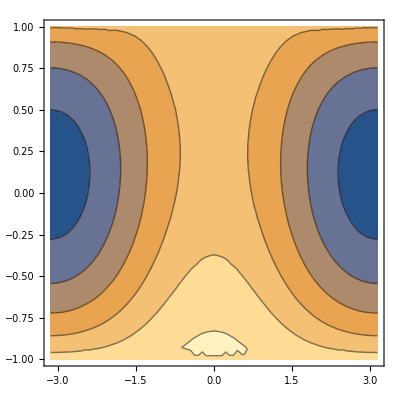

```mathematica
ContourPlot[hh/.{II->1,f->-0.2,δ->-0.03,R->1,p->-0.02,q->-0.5,r->0.02},{Φ, -π,π},{J, -1, 1}]
```

```mathematica
sol=Flatten[Solve[{ δ/R+(f J (1))/(2 √((II-J) (II+J)))==0},J]];
```

```mathematica
J1=(J/.{sol[[1]]}) +d j
```

d j-(2 II δ)/(√(f^2 R^2+4 δ^2))

```mathematica
Simplify[Series[1/4 ((4 δ)/R+(2 f J)/(√((II-J) (II+J))))/.{J->J1,II->1,f->-0.2,R->1,p->-0.02,q->-0.5,r->0.02,δ->-0.03},{d,0,2}]];
```

```mathematica
Coefficient[%44,d,2];
```

```mathematica
solPlot=Flatten[Solve[{ II (p-r)+J (p-2 q+r)+(4 δ)/R-(2 f J)/(√((II-J) (II+J)))==0/.{II->1,f->-0.2,R->1,p->-0.02,q->-0.5,r->0.02}},J]];
```

```mathematica
Jplot={J/.{solPlot[[1]]},J/.{solPlot[[2]]},J/.{solPlot[[3]]},J/.{solPlot[[4]]}};
```

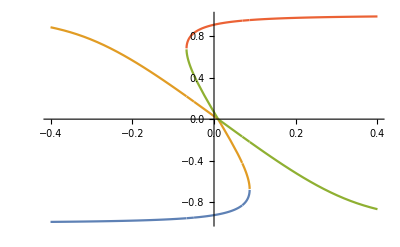

```mathematica
Plot[Jplot,{δ,-0.4,0.4}]
```

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→-0.943957-9.33782×10^-19 ⅈ,J→0.142438+1.47905×10^-17 ⅈ,J→0.348935-1.75238×10^-17 ⅈ,J→0.852584+3.66707×10^-18 ⅈ}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→-0.860094,J→0.834837,J→16.0126-10.0061 ⅈ,J→16.0126+10.0061 ⅈ}

```mathematica
ΦΦ=FullSimplify[D[hh,{Φ,2}]]
```

1/2 f √((II-J) (II+J)) Cos[Φ]

```mathematica
JJ = FullSimplify[D[hh,{J,2}]]
```

1/4 (p-2 q+r+(2 f II^2 Cos[Φ])/((II-J) (II+J))^(3/2))

```mathematica
ΦΦ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0756148

```mathematica
JJ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.241302

```mathematica
ΦΦ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0550497

```mathematica
JJ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.609426

```mathematica
JStr=-1/2η Sin[Θ] √((II-J[t]) (II+J[t])) Sin[Φ[t]]/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7};
ΦStr=1/4(II (p-r)+J [t](p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t]))))/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7};
```

```mathematica
plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-

```mathematica
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-

```mathematica
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black]
```

-Graphics3D-